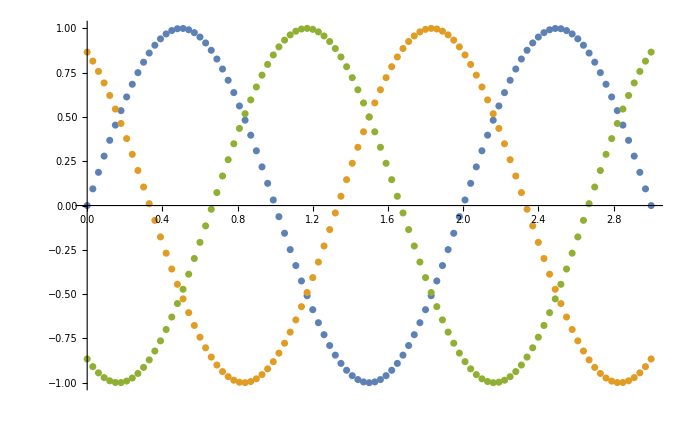

```mathematica
SS[offset_,length_,high_]:=Table[
{x,high*Sin[x*π+offset*π]},
{x,0,length,0.03}];
A1=SS[0,3,1];
A2=SS[2/3,3,1];
A3=SS[-2/3,3,1];
LL[x_]:=Line[{x,-1.1},{x,1.1}];
L1=LL[1/3 π];
AAA=ListPlot[{A1,A2,A3},GridLines->{{
{1/6,Green},
{2/6,Green},
{3/6,Green},
{4/6,Green},
{5/6,Green},
{7/6,Green},
{8/6,Green},
{9/6,Green},
{10/6,Green},
{11/6,Green},
{1,Red},
{2,Red},
{3,Red}
},None}]
```